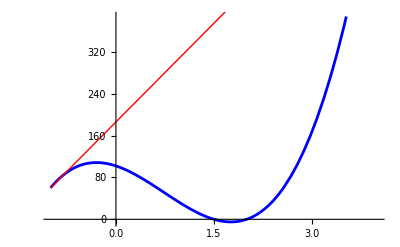

```mathematica
f[x_]= 26 x^3-57 x^2- 41x + 102;
a= -1;
b=4;
Plot[f[x],{x,-1,4}, PlotStyle->Blue, Epilog->{Red,Line[{{a,f[a]}, {b, f[b]}}]}]
```

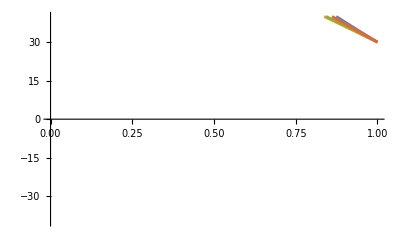

Решение х= 1.49935 Шаг= 6

```mathematica
f[x_]= 26 x^3-57 x^2- 41x + 102;
a=0;
b=1;

eps=0.001;
ex=eps*10;
If[f[a]*f''[a]>0,xn0=b;g[x_]:=a-(f[a]*(x-a)/(f[x]-f[a]));
hord[x_,xn_]:=f[xn]+((x-xn)/(xn-a)*(f[xn]-f[a])),xn0=a;g[x_]:=x-(f[x]*(b-x)/(f[b]-f[x]));
hord[x_,xn_]:=f[xn]+((x-xn)/(xn-b)*(f[xn]-f[b]))];

xn1=g[xn0];n=1;

While[ex>eps,If[n==2,Print[Plot[{f[x],hord[x,xn1],hord[x,xn0],hord[x,xn01]},{x,a,b},
Epilog->{Purple,Dashed,InfiniteLine[{xn1,0},{0,1}],InfiniteLine[{xn0,0},{0,1}],
PointSize[0.013],Point[{{xn0,0},{xn0,f[xn0]},{xn1,0},{xn1,f[xn1]},{g[xn1],0}}]},PlotRange->40]]];
xn01=xn0;xn0=xn1;
xn1=g[xn0];
ex=((xn1-xn0)^2)/(Abs[xn1+xn01-2 xn0]);
n=n+1;]
Print["Решение х= ",xn1//N," Шаг= ",n]
```

```mathematica
f1[x_] = x^6-3 x^5-9 x^4+19 x^3+12 x^2 -36x +16;
```

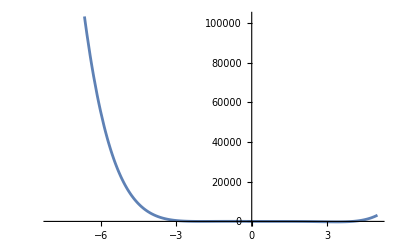

```mathematica
Plot[{f1[x]}, {x, -8, 5}]
```

```mathematica
Solve[f1[x]== 0 ]
```

{{x→-2},{x→-2},{x→1},{x→1},{x→1},{x→4}}

```mathematica
Nsolve[f1[x]==0]
```

Nsolve[16-36 x+12 x^2+19 x^3-9 x^4-3 x^5+x^6==0]

```mathematica
Simplify[Nsolve[6 x^5+x^6==0]]
```

Nsolve[x (6+x)==0]

```mathematica
Roots[f1[x] == 0, x]
```

x==-2||x==-2||x==1||x==1||x==1||x==4

```mathematica
Factor[f1[x]]
```

(-4+x) (-1+x)^3 (2+x)^2

```mathematica
FindRoot[f1[x]== 0, {x, -6}]
```

{x→-2.}

```mathematica
{x->-6.}
```

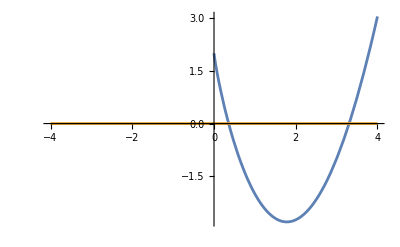

```mathematica
f[x_]= x*Log[3,x] + x^2  - 5x +2;
g[x_] = 0;

Plot[{f[x],g[x]},{x,-4,4}]
```

```mathematica
f2[x_]=x*Log[3,x] + x^2  - 5x +2;
a = 1; b=2; e = 0.001;
x1 = a;
Do[x2= x1;
x1 = (x1-f2[x1]/f2'[x1])//N;
If[Abs[x2-x1]< e,
Print["Решение x = ",x2//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}]
```

Решение x = 0.358791 получено на 5 шаге.

```mathematica
a = 1; b=2; e = 0.001;
x1 = a;
f3[x_]=x*Log[3,x] + x^2  - 5x +2;
x2= b;
Do[
x3= x2;
x2=x2-(x2-x1)/(f3[x2]-f3[x1])*f3[x2]//N;
If[Abs[x3-x2]< e,
Print["Решение x = ",x3//N, " получено на ",n, " шаге."];
Break[]],
{n,1,100}
]
```

Решение x = 0.358418+0.000154685 ⅈ получено на 10 шаге.

```mathematica
f2[x_]=x*Log[3,x] + x^2  - 5x +2;
```

```mathematica
Clear[x,x1,x3];
f2[x_]= x*Log[3,x] + x^2  - 5x +2;
f2Prime[x_] = f2'[x];
x1=1;x3=2;n=0;e=0.001;
While[ Abs[(x3-x1)]>e,n++;x3=x1;
λ=1/f2Prime[x1]//N;
φ[x_]=x-λ*f2[x1]//N;
x1=φ[x1]//N;n++;]
Print["Решение x = ",x3//N," получено на ",n," шаге."];
```

Решение x = 0.358791 получено на 10 шаге.

```mathematica
Solve[f2[x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[2-5 x+x^2+(x Log[x])/Log[3]==0,x]

```mathematica
NSolve[f2[x]==0&&-10<x<10,x]
```

{{x→0.358796},{x→3.30658}}

```mathematica
Nsolve[f2[x]==0]
```

Nsolve[2-5 x+x^2+(x Log[x])/Log[3]==0]

```mathematica
FindRoot[f2[x]== 0, {x, 0}]
```

{x→0.0796832}

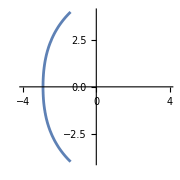

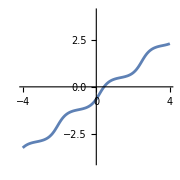

```mathematica
g1[x_,y_]=(x^2+y^2-2x)^2 -24(x^2+y^2);
g2[x_,y_]= Sin[2x+y]-4y+3x-2;

gr1= ContourPlot[g1[x,y]==0, {x,-4,4},{y,-4,4}, Axes->True, Frame->False,ImageSize->Small]
gr2 = ContourPlot[g2[x,y]==0, {x,-4,4},{y,-4,4}, Axes->True, Frame->False,ImageSize->Small]
```

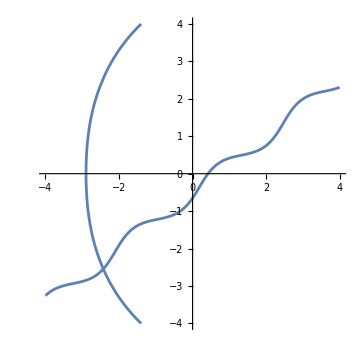

```mathematica
Show[gr1, gr2, ImageSize->Medium]
```

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,-0.3},{y,0.1}]
```

{x→0.212913,y→-0.113884}

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,1.2},{y,1}]
```

{x→1.74447,y→1.37337}

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,-0.3},{y,-0.1}]
```

{x→-0.318845,y→-0.315802}

```mathematica
FindRoot[{g1[x,y]==0, g2[x,y]==0},{x,1.2},{y,-1}]
```

{x→1.43746,y→-1.21268}